```mathematica
SetDirectory[NotebookDirectory[]];
```

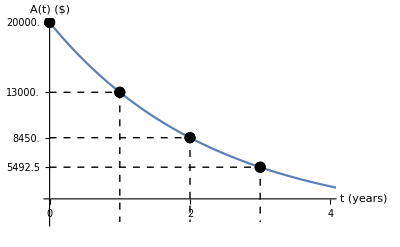

{depreciate.pdf,depreciate.svg}

```mathematica
f[x_]:=20000(0.65)^x;
Show[
Plot[f[x],{x,0,5}],
Graphics[{Black,Dashed,Line[{{0,f[1]},{1,f[1]},{1,0}}]}],
Graphics[{Black,Dashed,Line[{{0,f[2]},{2,f[2]},{2,0}}]}],
Graphics[{Black,Dashed,Line[{{0,f[3]},{3,f[3]},{3,0}}]}],
ListPlot[{{0,f[0]}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{1,f[1]}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{2,f[2]}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{3,f[3]}},PlotStyle->{Black,PointSize[0.02]}],
Ticks->{{0,1,2,3,4,5},{f[0],f[1],f[2],f[3]}},AxesStyle->Directive[16],AxesLabel->{"t (years)","A(t) ($)"},PlotRange->{{0,4},{0,20000}}
]
Export[{"depreciate.pdf","depreciate.svg"},%]
```

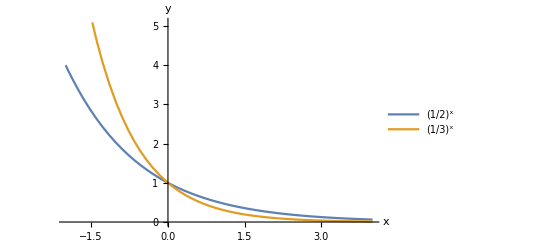

{expdecay.pdf,expdecay.svg}

```mathematica
Plot[{(1/2)^x,(1/3)^x},{x,-2,4},PlotLegends->"Expressions",AxesLabel->{"x","y"}]
Export[{"expdecay.pdf","expdecay.svg"},%]
```

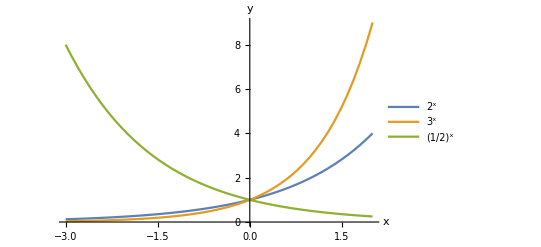

{exps.pdf,exps.svg}

```mathematica
Plot[{2^x,3^x,(1/2)^x},{x,-3,2},PlotLegends->"Expressions",AxesLabel->{"x","y"},AxesStyle->Directive[16]]
Export[{"exps.pdf","exps.svg"},%]
```

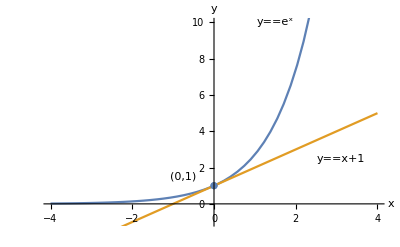

{expexp.pdf,expexp.svg}

```mathematica
Show[
Plot[{Exp[x],x+1},{x,-4,4},AxesStyle->Directive[16],AxesLabel->{"x","y"}],
ListPlot[{{0,1}}],
PlotRange->{{-4,4},{-1,10}},
Epilog->{
Style[Text[TraditionalForm[HoldForm["(0,1)"]],{-0.75,1.5}],16],
Style[Text[HoldForm[y==e^x],{1.5,10}],16],Style[Text[HoldForm[y==x+1],{3.1,2.5}],16]
}
]
Export[{"expexp.pdf","expexp.svg"},%]
```

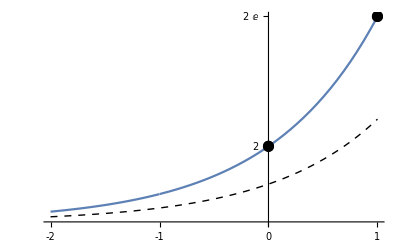

```mathematica
f[x_]:=2Exp[x]
Show[
Plot[Exp[x],{x,-2,1},PlotStyle->{Thin,Black,Dashed}],
Plot[f[x],{x,-2,1}],
ListPlot[{{0,f[0]}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{1,f[1]}},PlotStyle->{Black,PointSize[0.02]}],
Ticks->{Range[-2,2],{2,2Exp[1]}},PlotRange->{{-2,1},{0,2Exp[1]}},AxesStyle->Directive[16]
]
Export[{"expt1.pdf","expt1.svg"},%];
```

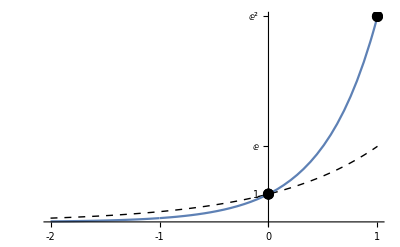

```mathematica
f[x_]:=Exp[2x]
Show[
Plot[Exp[x],{x,-2,1},PlotStyle->{Thin,Black,Dashed}],
Plot[f[x],{x,-2,1}],
ListPlot[{{0,f[0]}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{1,f[1]}},PlotStyle->{Black,PointSize[0.02]}],
Ticks->{Range[-2,2],{1,Exp[1],Exp[2]}},AxesStyle->Directive[16],PlotRange->{{-2,1},{0,Exp[2]}}
]
Export[{"expt2.pdf","expt2.svg"},%];
```

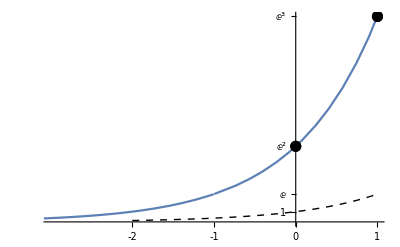

```mathematica
f[x_]:=Exp[x+2]
Show[
Plot[Exp[x],{x,-2,1},PlotStyle->{Thin,Black,Dashed}],
Plot[f[x],{x,-4,4}],
ListPlot[{{0,f[0]}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{1,f[1]}},PlotStyle->{Black,PointSize[0.02]}],
Ticks->{Range[-2,2],{1,Exp[1],Exp[2],Exp[3]}},AxesStyle->Directive[16],PlotRange->{{-3,1},{0,Exp[3]}}
]
Export[{"expt3.pdf","expt3.svg"},%];
```

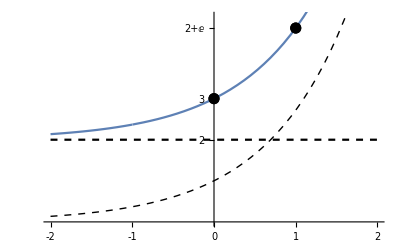

```mathematica
f[x_]:=Exp[x]+2
Show[
Plot[Exp[x],{x,-2,2},PlotStyle->{Thin,Black,Dashed}],
Plot[f[x],{x,-2,2}],
Plot[2,{x,-2,2},PlotStyle->{Black,Dashed}],
ListPlot[{{0,f[0]}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{1,f[1]}},PlotStyle->{Black,PointSize[0.02]}],
Ticks->{Range[-2,2],{3,2,f[1]}},AxesStyle->Directive[16],PlotRange->{{-2,2},{0,5}}
]
Export[{"expt4.pdf","expt4.svg"},%];
```

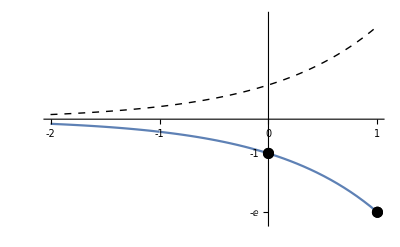

```mathematica
f[x_]:=-Exp[x]
Show[
Plot[Exp[x],{x,-2,1},PlotStyle->{Thin,Black,Dashed}],
Plot[f[x],{x,-2,1}],
ListPlot[{{0,f[0]}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{1,f[1]}},PlotStyle->{Black,PointSize[0.02]}],
Ticks->{Range[-2,2],{-1,-Exp[1]}},AxesStyle->Directive[16],PlotRange->{{-2,1},{-3,3}}
]
Export[{"expt5.pdf","expt5.svg"},%];
```

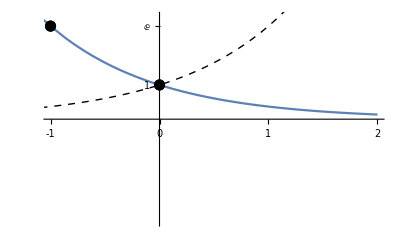

```mathematica
f[x_]:=Exp[-x]
Show[
Plot[Exp[x],{x,-2,2},PlotStyle->{Thin,Black,Dashed}],
Plot[f[x],{x,-2,2}],
ListPlot[{{0,f[0]}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{-1,f[-1]}},PlotStyle->{Black,PointSize[0.02]}],
Ticks->{Range[-2,2],{1,Exp[1]}},AxesStyle->Directive[16],PlotRange->{{-1,2},{-3,3}}
]
Export[{"expt6.pdf","expt6.svg"},%];
```

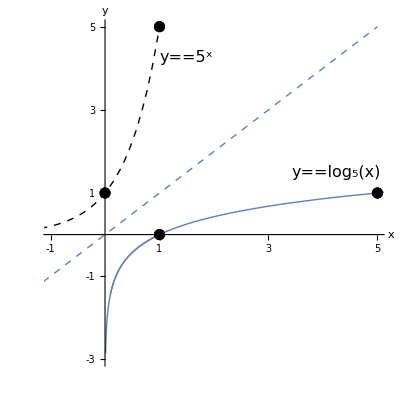

```mathematica
Show[
Plot[Log[5,x],{x,0.1,6},PlotStyle->{Thick},PlotPoints->100,MaxRecursion->2],
Plot[Log[5,x],{x,0.01,1},PlotStyle->{Thick},PlotPoints->100,MaxRecursion->2],
Plot[5^x,{x,-3,2},PlotStyle->{Thick,Black,Dashed}],
Plot[x,{x,-3,5},PlotStyle->{Thin,Dashed}],
ListPlot[{{1,0}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{5,1}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{0,1}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{1,5}},PlotStyle->{Black,PointSize[0.02]}],
AxesStyle->Directive[16],AxesLabel->{"x","y"},
Ticks->{Range[-1,5],Range[-5,5]},
PlotRange->{{-1,5},{-3,5}},AspectRatio->1,
Epilog->{Text[Style[ToExpression["y = \log_5(x)",TeXForm,HoldForm],16],{4.25,1.5}],Text[Style[ToExpression["y = 5^x",TeXForm,HoldForm],16],{1.5,4.25}]}]
Export[{"log5.pdf","log5.svg"},%];
```

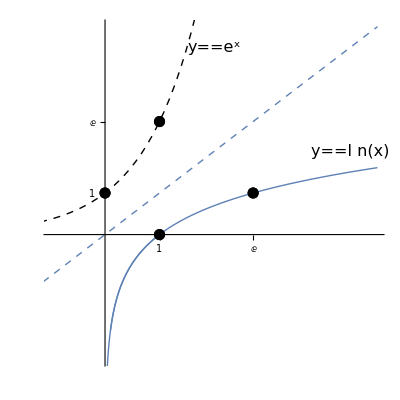

```mathematica
Show[
Plot[Log[x],{x,0.1,5},PlotStyle->{Thick},PlotPoints->100,MaxRecursion->2],
Plot[Log[x],{x,0.01,1},PlotStyle->{Thick},PlotPoints->100,MaxRecursion->2],
Plot[Exp[x],{x,-3,2},PlotStyle->{Thick,Black,Dashed}],
Plot[x,{x,-3,5},PlotStyle->{Thin,Dashed}],
ListPlot[{{1,0}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{Exp[1],1}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{0,1}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{1,Exp[1]}},PlotStyle->{Black,PointSize[0.02]}],
Epilog->{Text[Style[ToExpression["y = ln(x)",TeXForm,HoldForm],16],{4.5,2}],Text[Style[ToExpression["y = e^x",TeXForm,HoldForm],16],{2,4.5}]},
Ticks->{{1,Exp[1]},{1,Exp[1]}},
PlotRange->{{-1,5},{-3,5}},AspectRatio->1]
Export[{"logln.pdf","logln.svg"},%];
```

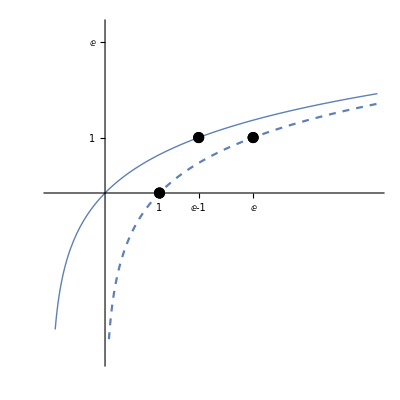

```mathematica
SetDirectory[NotebookDirectory[]];
Show[
Plot[Log[x+1],{x,-1.001,5},PlotStyle->{Thick},PlotPoints->100,MaxRecursion->2],
Plot[Log[x],{x,0.001,5},PlotStyle->{Dashed},PlotPoints->100,MaxRecursion->2],
ListPlot[{{1,0}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{Exp[1],1}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{Exp[1]-1,1}},PlotStyle->{Black,PointSize[0.02]}],

Ticks->{{1,Exp[1],Exp[1]-1},{1,Exp[1]}},
PlotRange->{{-1,5},{-3,3}},AspectRatio->1]
Export["lntrans.png",%];
```

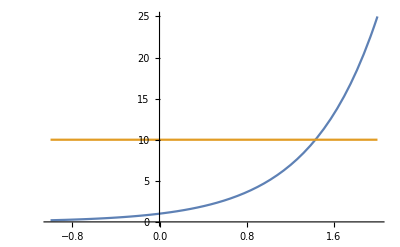

expsoln.png

```mathematica
Show[Plot[{5^x,10},{x,-1,2}]]
Export["expsoln.png",%]
```

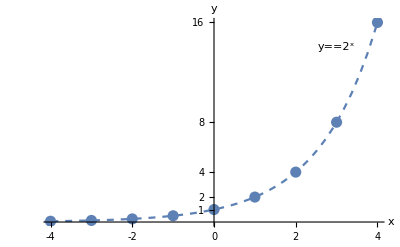

{doubling.svg,doubling.pdf}

```mathematica
Show[
ListPlot[Table[{k,2^k},{k,Range[-4,4]}],PlotStyle->{PointSize[0.02]}],
Plot[2^x,{x,-5,5},PlotStyle->Dashed],
AxesStyle->Directive[14],AxesLabel->{"x","y"},
Ticks->{Range[-4,4],{1,2,4,8,16}},
Epilog->{
Style[Text[HoldForm[y==2^x],{3,14}],16]
}]
Export[{"doubling.svg","doubling.pdf"},%]
```